```mathematica
B={{1,0,0,0,0},
    {1, 1, 0,0,0},
{1,0,1,0,0},
{1,0,1,1,0},
{1,0,1,0,1}}
```

{{1,0,0,0,0},{1,1,0,0,0},{1,0,1,0,0},{1,0,1,1,0},{1,0,1,0,1}}

```mathematica
MatrixForm[B]
```

(1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1)

```mathematica
T = {{0,1,1,0,0}, {0,0,0,0,0}, {0,0,0,1,1}, {0,0,0,0,0}, {0,0,0,0,0}}
```

{{0,1,1,0,0},{0,0,0,0,0},{0,0,0,1,1},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
MatrixForm[T]
```

(0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Inverse[B] // MatrixForm
```

(1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0
0 | 0 | -1 | 1 | 0
0 | 0 | -1 | 0 | 1)

```mathematica
IdentityMatrix[5] - Transpose[T] // MatrixForm
```

(1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0
0 | 0 | -1 | 1 | 0
0 | 0 | -1 | 0 | 1)

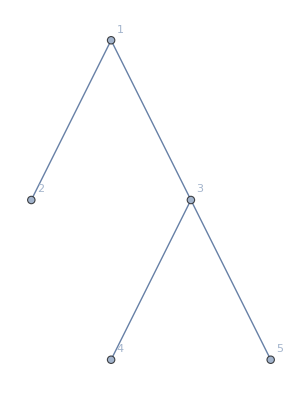

```mathematica
TreePlot[{1 -> 2, 1 -> 3, 3 -> 4, 3 -> 5}, Automatic, VertexLabels -> Automatic]
```

```mathematica
B//MatrixForm
```

(1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1)

```mathematica
(B . Transpose[B]) // MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 2 | 2
1 | 1 | 2 | 3 | 2
1 | 1 | 2 | 2 | 3)

```mathematica
u={0.2, 0.3, 0.1, 0.0, 0.4}
```

{0.2,0.3,0.1,0.,0.4}

```mathematica
u . B
```

{1.,0.3,0.5,0.,0.4}

```mathematica
u . B + RandomReal[NormalDistribution[0, 0.4]]
```

{0.512169,-0.187831,0.0121695,-0.487831,-0.0878305}

```mathematica
{0.64,0.44,0.34,0.2,0.24} . Inverse[B]
```

{-0.14,0.44,-0.1,0.2,0.24}

```mathematica
Inverse[(B . Transpose[B])]  // MatrixForm
```

(3 | -1 | -1 | 0 | 0
-1 | 1 | 0 | 0 | 0
-1 | 0 | 3 | -1 | -1
0 | 0 | -1 | 1 | 0
0 | 0 | -1 | 0 | 1)

```mathematica
Inverse[(B . Transpose[B])] // MatrixForm
```

(3 | -1 | -1 | 0 | 0
-1 | 1 | 0 | 0 | 0
-1 | 0 | 3 | -1 | -1
0 | 0 | -1 | 1 | 0
0 | 0 | -1 | 0 | 1)

```mathematica
{U, S, V} =  SingularValueDecomposition[Inverse[(B . Transpose[B])] ]
```

{1}
 |  |  |  |

```mathematica
U // N // MatrixForm
```

(0.614932 | -0.667488 | 0. | -0.316405 | 0.276055
-0.178459 | 0.371484 | 0. | -0.854397 | 0.316477
-0.710602 | -0.507107 | 0. | 0.104413 | 0.47643
0.206223 | 0.282226 | -0.707107 | 0.281949 | 0.546192
0.206223 | 0.282226 | 0.707107 | 0.281949 | 0.546192)

```mathematica
V // N // MatrixForm
```

(0.614932 | -0.667488 | 0. | -0.316405 | 0.276055
-0.178459 | 0.371484 | 0. | -0.854397 | 0.316477
-0.710602 | -0.507107 | 0. | 0.104413 | 0.47643
0.206223 | 0.282226 | -0.707107 | 0.281949 | 0.546192
0.206223 | 0.282226 | 0.707107 | 0.281949 | 0.546192)

```mathematica
S // N // MatrixForm
```

(4.44579 | 0. | 0. | 0. | 0.
0. | 2.79682 | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0.629674 | 0.
0. | 0. | 0. | 0. | 0.127724)

```mathematica
(B . Transpose[B]) // MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 2 | 2
1 | 1 | 2 | 3 | 2
1 | 1 | 2 | 2 | 3)